## Computing p(χ_eff = 0) with numerical values Maria Okounkova

```mathematica
First let's compute p(Subscript[χ, eff]| q, ℳ) = 0
```

```mathematica
SolutionM = Solve[m1 + m2 == M &&  m1/m2 == q,{m1,m2}]
```

{{m1→(M q)/(1+q),m2→M/(1+q)}}

#### χ_eff in terms of {q, ℳ}

```mathematica
Solutionm1m2 = Solve[((m1*m2)^(3/5) / (m1 + m2)^(1/5))== ℳ  &&  m1/m2 == q,{m1,m2}]
```

{{m1→q^(2/5) (1+q)^(1/5) ℳ,m2→((1+q)^(1/5) ℳ)/q^(3/5)},{m1→-(-1)^(1/5) q^(2/5) (1+q)^(1/5) ℳ,m2→-((-1)^(1/5) (1+q)^(1/5) ℳ)/q^(3/5)},{m1→(-1)^(2/5) q^(2/5) (1+q)^(1/5) ℳ,m2→((-1)^(2/5) (1+q)^(1/5) ℳ)/q^(3/5)},{m1→-(-1)^(3/5) q^(2/5) (1+q)^(1/5) ℳ,m2→-((-1)^(3/5) (1+q)^(1/5) ℳ)/q^(3/5)},{m1→(-1)^(4/5) q^(2/5) (1+q)^(1/5) ℳ,m2→((-1)^(4/5) (1+q)^(1/5) ℳ)/q^(3/5)}}

```mathematica
Subm1m2 = Solutionm1m2[[1]]
```

{m1→q^(2/5) (1+q)^(1/5) ℳ,m2→((1+q)^(1/5) ℳ)/q^(3/5)}

```mathematica
ChiEffectivem1m2 = (a1 * (Cos[θ1]/m1) + (a2 * Cos[θ2])/m2)/(m1 + m2)
```

((a1 Cos[θ1])/m1+(a2 Cos[θ2])/m2)/(m1+m2)

```mathematica
ChiEffective =ChiEffectivem1m2 /. Subm1m2 // FullSimplify
```

(q^(1/5) (a1 Cos[θ1]+a2 q Cos[θ2]))/((1+q)^(7/5) ℳ^2)

```mathematica
ChiEffectiveM =ChiEffectivem1m2 /. SolutionM // FullSimplify
```

{((1+q) (a1 Cos[θ1]+a2 q Cos[θ2]))/(M^2 q)}

#### Prior distributions

```mathematica
Pa[a_] := 1
Pθ[θ_] := Sin[θ]/2
Pϕ[ϕ_] := 1/(2*Pi)
Pℳ[ℳ_] := 1/(40 - 25)
PriorProduct = Pa[a1]*Pa[a2]*Pθ[θ1]*Pθ[θ2]*Pϕ[ϕ1]*Pϕ[ϕ2] (*Pℳ[ℳ]*)
```

(Sin[θ1] Sin[θ2])/(16 π^2)

#### Conditional probability p(χ_eff = 0 | a_1, a_2, θ_1, θ_2, ϕ_1, ϕ_2, q, ℳ)

```mathematica
PChiEffGivenAllVariables = DiracDelta[ChiEffective]
```

DiracDelta[(q^(1/5) (a1 Cos[θ1]+a2 q Cos[θ2]))/((1+q)^(7/5) ℳ^2)]

Use the identity δ(Ax) = δ(x) / |A| for scalar A 
(see https://en.wikipedia.org/wiki/Dirac_delta_function#Scaling_and_symmetry)

```mathematica
PChiEffGivenAllVariablesRescaled = (1+q)^(7/5) ℳ^2 / q^(1/5) * DiracDelta[(a1 Cos[θ1]+a2 q Cos[θ2])]
```

((1+q)^(7/5) ℳ^2 DiracDelta[a1 Cos[θ1]+a2 q Cos[θ2]])/q^(1/5)

#### Create integrand to compute the probability p(χ_eff = 0| q, ℳ)

```mathematica
Integrand = PChiEffGivenAllVariablesRescaled * PriorProduct
```

((1+q)^(7/5) ℳ^2 DiracDelta[a1 Cos[θ1]+a2 q Cos[θ2]] Sin[θ1] Sin[θ2])/(16 π^2 q^(1/5))

#### Analytically Integrate over ϕ_1, ϕ_2, ℳ, and θ_1

```mathematica
Integrandϕ = Integrate[Integrand, {ϕ1, 0, 2*Pi}, {ϕ2, 0, 2*Pi}]
```

((1+q)^(7/5) ℳ^2 DiracDelta[a1 Cos[θ1]+a2 q Cos[θ2]] Sin[θ1] Sin[θ2])/(4 q^(1/5))

```mathematica
(*Integrandϕℳ = Integrate[Integrandϕ, {ℳ, 25, 40}]*)
```

(16125 (1+q)^(7/5) DiracDelta[a1 Cos[θ1]+a2 q Cos[θ2]] Sin[θ1] Sin[θ2])/(4 q^(1/5))

```mathematica
Integrandϕθ1 = Integrate[Integrandϕ , {θ1, 0, Pi}]
```

-((1+q)^(7/5) ℳ^2 (HeavisideTheta[-a1+a2 q Cos[θ2]]-HeavisideTheta[a1+a2 q Cos[θ2]]) Sin[θ2])/(4 a1 q^(1/5))

```mathematica
(*Integrandϕℳθ1 = Integrate[Integrandϕℳ , {θ1, 0, Pi}]*)
```

-1/(4 a1 q^(1/5))16125 (1+q)^(7/5) (HeavisideTheta[-a1+a2 q Cos[θ2]]-HeavisideTheta[a1+a2 q Cos[θ2]]) Sin[θ2]

#### Set up to Integrate numerically

Let’s remove the coefficient in front to simplify things - we’ll multiply the result by it later

```mathematica
PChieffZeroGivenQ[qval_] := NIntegrate[(Integrandϕθ1/.{q-> qval, ℳ -> 1}), {θ1, 0.0, Pi}, {θ2, 0.0, Pi}, {a1, 0.0, 1.0}, {a2, 0.0, 1.0}]
```

```mathematica
Now let's compute p(Subscript[χ, eff] | q) = 0 for various values of q
```

We define q to be uniform in [0.2, 1.0]

```mathematica
qvals = Range[0.25, 1.0, 0.01]
```

{0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.}

```mathematica
PChieffZeroGivenQ[1.0]
```

8.10239

```mathematica
PChieffGivenqvals = PChieffZeroGivenQ[qvals]
```

{10.6586,10.6556,7.88703,7.85174,7.81651,7.81506,7.81479,7.81834,7.79314,7.79983,7.79917,7.78174,7.80042,7.8098,7.76701,7.74903,7.75002,7.7547,7.76261,7.76474,7.75835,7.77166,7.75293,7.75167,7.76473,7.75683,7.75949,7.76724,7.75961,7.77569,7.75282,7.75971,7.7676,7.74737,7.76424,7.77566,7.77554,7.80079,7.82556,7.83533,7.83107,7.82505,7.8308,7.854,7.85122,7.87518,7.85962,7.88041,7.90261,7.93169,7.96182,7.96356,7.99488,7.94836,7.94803,7.94859,7.95794,7.96914,7.99683,7.97879,7.98867,8.0061,7.99382,8.03231,8.03782,8.03767,8.04445,8.06811,8.06587,8.05009,8.05518,8.06928,8.09221,8.12812,8.11651,8.10239}

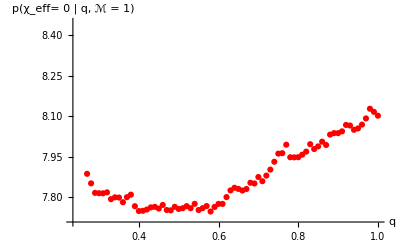

```mathematica
ListPlot[Transpose[{qvals,PChieffGivenqvals}], AxesLabel-> {"q", "p(χ_eff= 0 | q, ℳ = 1)"}, LabelStyle->Directive[Bold, Medium], PlotStyle->{Red, Thick}]
```